-Graphics3D-

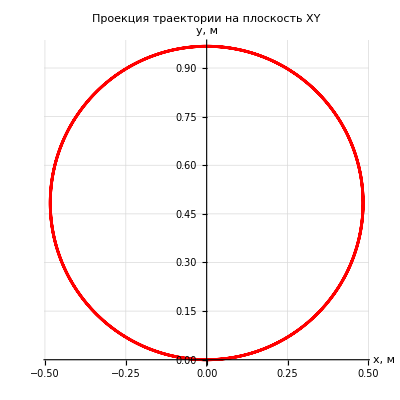

```mathematica
q=3.2*10^-19;
m=6.7*10^-27;
v=4000*10^3;
B=0.15;
alpha=60 Degree;

(*Выбор системы координат: ось Z вдоль B*)

vParallel=v*Cos[alpha];  (*составляющая вдоль B*)
vPerp=v*Sin[alpha];      (*перпендикулярная составляющая*)

(*Физические характеристики движения*)
omega=q*B/m;      (*циклотронная частота*) (*Циклотронная частота — частота обращения заряженной частицы в постоянном магнитном поле в плоскости,перпендикулярной вектору поля.*)
R=vPerp/omega;           (*ларморовский радиус*)
T=2*Pi/omega;          (*период вращения*)
h=vParallel*T;           (*шаг спирали*)

(*Print["=== ПАРАМЕТРЫ ДВИЖЕНИЯ ==="];
Print["Циклотронная частота ω = ",omega," рад/с"];
Print["Период вращения T = ",T," с"];
Print["Радиус спирали R = ",R," м"];
Print["Шаг спирали h = ",h," м"];*)

(*Аналитическое решение:закон движения*)
(*Для положительного заряда (q>0) и начальных условий:*)
(*в момент t=0:x=0,y=0,z=0;vx=vPerp,vy=0,vz=vParallel*)
x[t_]:=R*Sin[omega*t]
y[t_]:=R*(1-Cos[omega*t])
z[t_]:=vParallel*t

(*Время моделирования:несколько периодов*)
tMax=3*T;

trajectory=ParametricPlot3D[{x[t],y[t],z[t]},{t,0,tMax},PlotStyle->{Blue,Thickness[0.005]},PlotRange->All,AxesLabel->{"x, м","y, м","z, м"},LabelStyle->{FontFamily->"Times",FontSize->12},PlotLabel->Style["Траектория альфа-частицы в магнитном поле",14,Bold], BoxRatios->{1,1,1},ImageSize->500];

(*Проекция на плоскость XY (перпендикулярную B)*)
projectionXY=ParametricPlot[{x[t],y[t]},{t,0,tMax},PlotStyle->{Red,Thickness[0.005]},AspectRatio->1,AxesLabel->{"x, м","y, м"},LabelStyle->{FontFamily->"Times",FontSize->12},PlotLabel->Style["Проекция траектории на плоскость XY",14,Bold],GridLines->Automatic,ImageSize->400];


(*3D графики*)
trajectory
projectionXY
```

```mathematica
x[t_]:=R Cos[omega t]
y[t_]:=R Sin[omega t]
z[t_]:=vParallel t

rotationMatrix[w_,t_]:={{Cos[w t],-Sin[w t],0},{Sin[w t],Cos[w t],0},{0,0,1}} 
r[t_]:={x[t],y[t],z[t]} 

rNew[w_, t_] := r[t].rotationMatrix[w, t]

xNew[w_,t_]:=rNew[w,t][[1]]
yNew[w_,t_]:=rNew[w,t][[2]]
zNew[w_,t_]:=rNew[w,t][[3]]

(* Случай 1 *)
w1 = 1.25 omega;

trajectory1=ParametricPlot3D[{xNew[w1,t],yNew[w1,t],zNew[w1,t]},{t,0,tMax},PlotStyle->{Green,Thickness[0.005]},PlotRange->All,AxesLabel->{"x, м","y, м","z, м"},LabelStyle->{FontFamily->"Times",FontSize->12},PlotLabel->Style["Случай 1: w = 1.25 omega",14,Bold], BoxRatios->{1,1,1},ImageSize->500];

trajectory1

(* Случай 2 *)

w2 = 0.2 omega;

trajectory2=ParametricPlot3D[{xNew[w2,t],yNew[w2,t],zNew[w2,t]},{t,0,tMax},PlotStyle->{Purple,Thickness[0.005]},PlotRange->All,AxesLabel->{"x, м","y, м","z, м"},LabelStyle->{FontFamily->"Times",FontSize->12},PlotLabel->Style["Случай 2: w = omega / 5",14,Bold], BoxRatios->{1,1,1},ImageSize->500];

trajectory2

(* Случай 3 *)

trajectory3=ParametricPlot3D[{xNew[omega,t],yNew[omega,t],zNew[omega,t]},{t,0,tMax},PlotStyle->{Purple,Thickness[0.005]},PlotRange->All,AxesLabel->{"x, м","y, м","z, м"},LabelStyle->{FontFamily->"Times",FontSize->12},PlotLabel->Style["Случай 3: w = omega",14,Bold], BoxRatios->{1,1,1},ImageSize->500]

(* Случай 4 *)

w4 = -omega

trajectory3=ParametricPlot3D[{xNew[w4,t],yNew[w4,t],zNew[w4,t]},{t,0,tMax},PlotStyle->{Purple,Thickness[0.005]},PlotRange->All,AxesLabel->{"x, м","y, м","z, м"},LabelStyle->{FontFamily->"Times",FontSize->12},PlotLabel->Style["Случай 3: w = -omega",14,Bold], BoxRatios->{1,1,1},ImageSize->500];


trajectory3
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

-7.16418×10^6

-Graphics3D-